```mathematica
n=W*hbar*w0^3*tau/(Pi^2*c^2);
```

```mathematica
numbers={W->1/60,
hbar->1.05457182×10^(-34),
w0->2*Pi*(3*10^8)/(590*10^(-9)),
e0->8.858*10^(-12),
c->3*10^8,
tau->16*10^(-9),
kB->1.380649×10^(-23)};
```

```mathematica
n/.numbers
```

1.0324×10^-15

```mathematica
Solve[n==1/(Exp[hbar*w0/(kB*T)]-1),T]/.numbers
```

{{T→ConditionalExpression[24402.9/(34.5069+2 ⅈ π C[1]), C[1]∈ℤ]}}

```mathematica
24402.93093599141/34.50688565171109
```

707.19

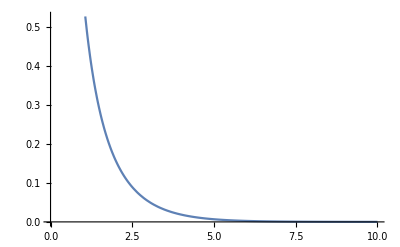

```mathematica
Plot[1/(Exp[x]-1),{x,0,10}]
```

```mathematica
g0=4*o^3*(muB)^2/(3*hbar*c^3);
```

```mathematica
num2={o->2*Pi*(3*10^10)/(21),
muB->9.27400999×10^(-21),
e0->8.858*10^(-12),
hbar->1.05457182×10^(-27),
c->3*10^10};
```

```mathematica
g0/.num2
```

2.91259×10^-15

```mathematica
1/(g0)/.num2
```

3.43337×10^14

```mathematica
(*convert seconds to years*)
```

```mathematica
(3.433369824006782*^14)/(365*24*60*60)
```

1.08871×10^7

```mathematica
(*problem 2*)
```

```mathematica
A=2*al*hbar*o21^2*0.64*(2*1/2+1)/(2*3/2+1)/(m*c^2);
```

```mathematica
Anew=2*al*hbar*o21^2/(m*c^2);
```

```mathematica
num3={al->1/137,
hbar->1.05457182×10^(-27),
o21->2*Pi*(3*10^8)/(590*10^(-9)),
m->9.10938370*10^(-28),
c->3*10^10};
```

```mathematica
A/.num3
```

6.13341×10^7

```mathematica
1/A/.num3
```

1.63041×10^-8

```mathematica
Anew/.num3
```

1.91669×10^8

```mathematica
1/Anew/.num3
```

5.21732×10^-9

```mathematica
A12=2*al*hbar*o21^2*0.32*(2*1/2+1)/(2*1/2+1)/(m*c^2);
```

```mathematica
1/A12/.num3
```

1.63041×10^-8

```mathematica
Isat=hbar*o*1.916691904049147*^8/(3*lam^2/(2*Pi))/.{hbar->1.05457182×10^(-34),lam->(590*10^(-9)),o->2*Pi*3*10^8/(590*10^(-9))}
```

388.537